```mathematica
ClearAll["Global`*"]
```

```mathematica
resultsPath="/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/double-beta-pairing-strength/parent-nuclei/results";
```

### Experimental data

```mathematica
ydataP={0.36,0.34,0.18,0.38,0.20,0.27,0.27,0.24};
ydataN={0.38,0.36,0.433,0.36,0.245,0.22,0.24,0.26};
xdata={76,82,96,100,116,128,130,150};
xdataL=1/#&@xdata;
expdataP=Table[{1/xdata[[i]],ydataP[[i]]},{i,1,Length[xdata]}];
expdataN=Table[{1/xdata[[i]],ydataN[[i]]},{i,1,Length[xdata]}];
```

### Plot style

```mathematica
mystyle = {Frame -> True, Axes -> False, FrameStyle -> Directive[Black, Thick], 
    LabelStyle -> {23, Bold, Black, FontFamily -> "Times"}, AspectRatio -> 0.8, 
    PlotRange->{0,0.5},ImageSize->350};
```

### Model

```mathematica
(*the pairing strength for protons*)
gp[a_,b_,x_]:=b+a*x;
(*the pairing strength for protons*)
gn[c_,d_,x_]:=d+c*x;
(*Perform the fitting procedure *)
protonParams=Values@FindFit[expdataP,b+a*x,{a,b},x];
neutronParams=Values@FindFit[expdataN,d+c*x,{c,d},x];
ydataPth=Table[gp[protonParams[[1]],protonParams[[2]],xdataL[[i]]],{i,1,Length[xdataL]}];
ydataNth=Table[gn[neutronParams[[1]],neutronParams[[2]],xdataL[[i]]],{i,1,Length[xdataL]}];
```

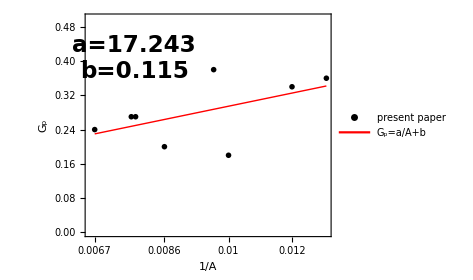

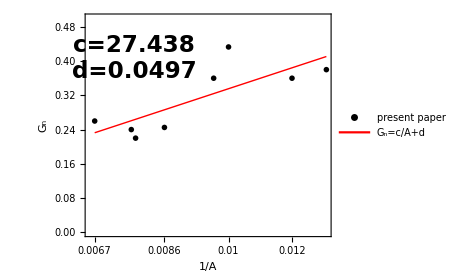

```mathematica
figP=ListPlot[{expdataP,Table[{xdataL[[i]],gp[protonParams[[1]],protonParams[[2]],xdataL[[i]]]},{i,1,Length[xdataL]}]},Evaluate[mystyle],PlotLegends->Placed[{"present paper","G_p=a/A+b"},{0.69,0.15}],Joined->{False, True},PlotMarkers->{{"●",Scaled[0.05]},None},PlotStyle->{{Black},{Red,Thick}},FrameLabel->{"1/A","G_p"},FrameTicks->{{Automatic,None},{{SetPrecision[N[xdataL[[2]]],2],SetPrecision[N[xdataL[[3]]],2],SetPrecision[N[xdataL[[5]]],2],SetPrecision[N[xdataL[[8]]],2]},None}},Epilog->{Inset[Style[StringTemplate["a=``\nb=``"][SetPrecision[protonParams[[1]],5],SetPrecision[protonParams[[2]],3]],23,Bold,Black,FontFamily->"Times"],Scaled[{0.2,0.8}]]}];
figN=ListPlot[{expdataN,Table[{xdataL[[i]],gn[neutronParams[[1]],neutronParams[[2]],xdataL[[i]]]},{i,1,Length[xdataL]}]},Evaluate[mystyle],PlotLegends->Placed[{"present paper","G_n=c/A+d"},{0.69,0.15}],Joined->{False, True},PlotMarkers->{{"●",Scaled[0.05]},None},PlotStyle->{{Black},{Red,Thick}},FrameLabel->{"1/A","G_n"},Epilog->{Inset[Style[StringTemplate["c=``\nd=``"][SetPrecision[neutronParams[[1]],5],SetPrecision[neutronParams[[2]],3]],23,Bold,Black,FontFamily->"Times"],Scaled[{0.2,0.8}]]},FrameTicks->{{Automatic,None},{{SetPrecision[N[xdataL[[2]]],2],SetPrecision[N[xdataL[[3]]],2],SetPrecision[N[xdataL[[5]]],2],SetPrecision[N[xdataL[[8]]],2]},None}}];
Show[figP]
Show[figN]
Export[StringTemplate["``/Gp.pdf"][resultsPath],figP];
Export[StringTemplate["``/Gn.pdf"][resultsPath],figN];
```

```mathematica
rms[data_,datath_]:=Sqrt[1/Length[data]*Sum[(data[[i]]-datath[[i]])^2/data[[i]],{i,1,Length[data]}]];
rmsP=rms[ydataP,ydataPth];
rmsN=rms[ydataN,ydataNth];
```